## Installations

### Initializations

```mathematica
Clear["Global`*"]
Needs["SymbolicC`"];
targetDir=NotebookDirectory[];
SetDirectory[targetDir];
```

### Install Packages: NBodyProblem.

```mathematica
MyPackageDirectory=ToFileName[{ParentDirectory[ParentDirectory[]],"Packages"}]
```

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/2-Atala/1-IRK Kodeak/4-Artikulurako-I/41-C (Artikulurako inplementazioa)/Packages/

```mathematica
Get["NBodyProblem`",Path->MyPackageDirectory];
Get["MyFunctions`",Path->MyPackageDirectory];
```

### Plot Style

```mathematica
StyleQuad=Red;
StyleIdeal=Orange;
StyleMachine=Lighter[Blue,.6];
StyleClassic=Lighter[Gray,.6];
StyleHairer=Green;
StyleError=Lighter[Blue,.6];
StyleEstimation=Orange;
StyleHamT12=Directive[Dashed,Red];
MarkerQuad="○"; (*○  △    □*)
MarkerIdeal="▲"; (*●  ▲  ■*)
MarkerMachine="■";
```

## Filenames

### Paths

```mathematica
DataDirectory="Data/";
ImagesDirectory="Images/";
```

### Input Files

```mathematica
filey0=NotebookDirectory[]<>DataDirectory<>"Datay0.bin";
fileA=NotebookDirectory[]<>DataDirectory<>"outA.bin";
fileTerminal=NotebookDirectory[]<>DataDirectory<>"Output.bin";
```

### Output Files

```mathematica
esperiment="NBODY";
(* energy error*)
plot1=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"3A.pdf";
plot1b=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"3B.pdf";
plot11=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"plot11.pdf";

(* distribution of energy jumps*)
plot4=NotebookDirectory[]<>ImagesDirectory<>esperiment<>"2A.pdf";
```

## Parameters (OSS)

### Problem parameters and initial values

```mathematica
prec=100;
n=6;
neq=36;
```

```mathematica
q={0.,0.,0.,
-3.5023653,-3.8169847,-1.5507963,
9.0755314,-3.0458353,-1.6483708,
8.3101420,-16.2901086,-7.2521278,
11.4707666,-25.7294829,-10.8169456,
-15.5387357,-25.2225594,-3.1902382};

v={0.,0.,0.,
0.00565429,-0.00412490,-0.00190589,
0.00168318,0.00483525,0.00192462,
0.00354178,0.00137102,0.00055029,
0.00288930,0.00114527,0.00039677,
0.00276725,-0.00170702,-0.00136504};
```

```mathematica
u=Flatten[{q,v}];
```

```mathematica
G=2.95912208286*10^-4;
m[1]=1.00000597682;
m[2]=0.000954786104043;
m[3]=0.000285583733151;
m[4]=0.0000437273164546;
m[5]=0.0000517759138449;
m[6]=1.0/(1.3*10^8);
Gm=Table[G*m[i],{i,1,n}];
(* sun, Jupiter, Saturn, Uranus, Neptune, Pluto *)
```

```mathematica
orderplanets= Sort[Range[n],Abs[Gm[[#1]]]< Abs[Gm[[#2]]]&]-1
```

{5,3,4,2,1,0}

```mathematica
preal=parameters=Gm;
pint=orderplanets;
```

```mathematica
u0=Chdata[u,preal];
u0D=N[u0];
u0DD=SetPrecision[u0D,prec];
ee0 =u0 - u0DD;
```

### Integration parameters.

```mathematica
h=500./3;
t0=0.;tend=h*60000;
sampling=120;
```

```mathematica
codfun0=2; (*NBody Problem*)

ns= 6;
nstep=(tend-t0)/h
nout=nstep/sampling
```

60000.

500.

### RKG parameters

```mathematica
neq=Length[u0];
prec=100;
HAM=NBodyHam;
HAM2=NBodyHam3;
ERR=ErrorPosition;
ERRFORTRAN=ErrorPositionFortranOSS;
```

## Import (math execution)

```mathematica
Now
```

Sun 29 Jan 2017 17:32:21GMT+1.

```mathematica
nstat=10;
```

### Parameters

```mathematica
noutA=Round[nout]+1;
step=1;
dd1= (2neq+1);
dd2= (3neq+1);
dd3=neq+1;
```

### Import

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileA,"Real64"],{nstat,noutA,dd1}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpA=Map[First,Partition[tpA,step]];
{Length[outA],Length[outA[[1]]]}
```

{1,501}

## Import (terminal execution)

```mathematica
Now
```

Sun 29 Jan 2017 17:33:31GMT+1.

```mathematica
nstat=1;
```

### Parameters

```mathematica
noutA=Round[nout]+1;
step=1;
dd1= (2neq+1);
dd2= (3neq+1);
dd3=neq+1;
```

### Import

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileTerminal,"Real64"],{nstat,noutA,dd1}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpA=Map[First,Partition[tpA,step]];
{Length[outA],Length[outA[[1]]]}
```

{1,501}

## Analisis-I

```mathematica
Now
```

Sun 29 Jan 2017 17:33:38GMT+1.

### Graphics-I (Energy): Plot1, Plot2

```mathematica
{MeanHamA,DesvHamA}=FunEnergy[outA, nstat,noutA,HAM, preal,neq,prec,step] ;
```

```mathematica
eskala=10^(15);
MeanHamAdata = Transpose[{tpA,MeanHamA*eskala}];
DesvHamAdata = Transpose[{tpA,DesvHamA*eskala}];
```

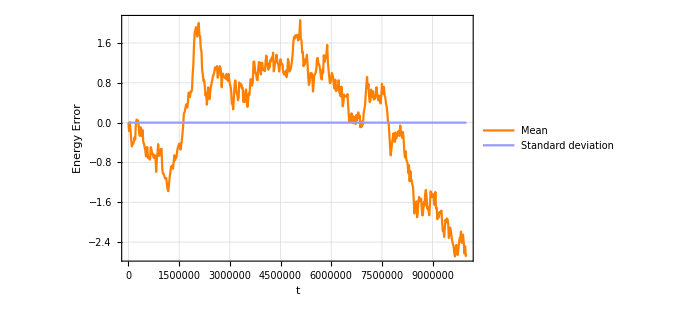

```mathematica
plot=ListPlot[{MeanHamAdata,DesvHamAdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
PlotLegends->Placed[{"Mean","Standard deviation"},Below],
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot1,Show[plot] ];
```

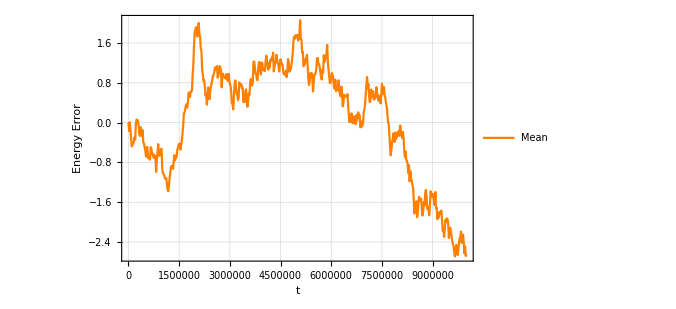

```mathematica
plot=ListPlot[{MeanHamAdata},AxesLabel->{"t","Energia"},Joined->True,
PlotRange->All,
PlotLegends->Placed[{"Mean"},Below],
PlotTheme->"Detailed",
ImageSize->500,
PlotStyle->{StyleIdeal},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","Energy Error"},
LabelStyle->Directive[Black,Bold]
]
Export[plot1b,Show[plot] ];
```

### Graphics-I (Energy-2): Plot11.

```mathematica
maxnstat=100;
If[nstat<maxnstat,nstat0=nstat,nstat0=maxnstat];
```

```mathematica
AllHamerrA=FunAllEnergy[outA, nstat0,noutA,HAM, parameters,neq,prec,step] ;
```

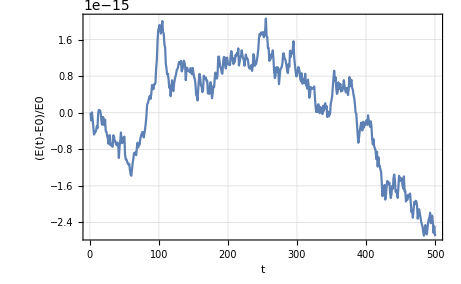

```mathematica
plot=ListPlot[Table[AllHamerrA[[i]],{i,nstat0}],AxesLabel->{"t","(E(t)-E0)/E0"},Joined->True,
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},
Frame->True,FrameLabel->{"t","(E(t)-E0)/E0"}]
Export[plot11,Show[plot] ];
```

### Graphics-III (Histogram) : Plot4, Plot5

```mathematica
HamerrA=FunHamErrDif[outA,nstat,noutA,HAM, parameters,neq,prec,step] ;
```

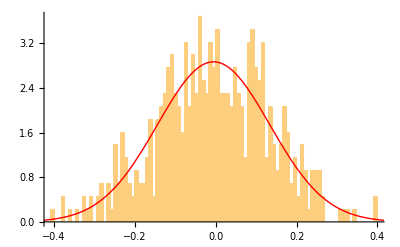

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/2-Atala/1-IRK Kodeak/4-Artikulurako-I/41-C (Artikulurako inplementazioa)/Examples/OSS/Images/NBODY2A.pdf

```mathematica
Hamerdif=HamerrA 10^15;
μ=Mean[Hamerdif];
σ=StandardDeviation[Hamerdif];
ir1=Histogram[Hamerdif,{σ/16},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[plot4,Show[ir1,ir2]]
```

```mathematica
MaxDE=Max[Abs[MeanHamA]]//N;
Hamerdif=Drop[MeanHamA ,1]-Drop[ MeanHamA,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
{MaxDE,μ,σ}
```

{2.6875×10^-15,-5.31011×10^-18,1.39121×10^-16}